## Generating 5-fold symmetry axis on 2D surface

n= 1

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
```

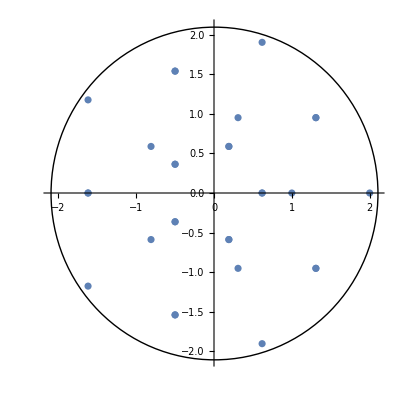

```mathematica
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
n1point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4], AspectRatio->1];
circle = Graphics[Circle[{0, 0}, 2.1]];
n1 = Show[n1point, circle, PlotRange-> All]
```

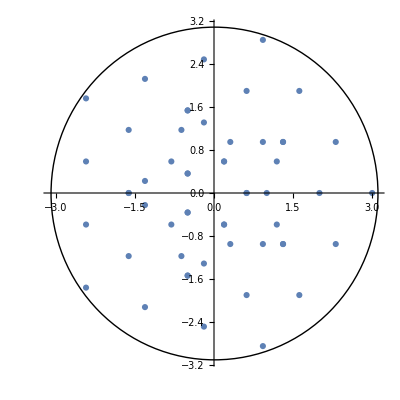

-Graphics-

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
transv2 = {{a1+2,-c1}, {1+2,0}, {a1+2,c1}, {-b1+2,d1}, {-b1+2,-d1}};
rotv5 = RotationTransform[2π/5, {0,0}] /@ # &@transv2;
rotv6 = RotationTransform[2π/5, {0,0}] /@ # &@rotv5;
rotv7 = RotationTransform[2π/5, {0,0}] /@ # &@rotv6;
rotv8 = RotationTransform[2π/5, {0,0}] /@ # &@rotv7;
n2point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8], AspectRatio->1];
circle2 = Graphics[Circle[{0, 0}, 3.1]];
n2 = Show[n2point, circle2, PlotRange-> All]
```

## Loading data

import data as string:

```mathematica
data =Import[URLDownload["https://files.rcsb.org/download/3J3I.pdb1.gz"],"String"];
```

replace negative signs(-) with spaces to separate columns:

```mathematica
spaced  = StringReplace[data,"-"-> " -"];
```

export modified file to directory as text:

```mathematica
Export["/Users/Jihyeon/Desktop/3J3I_spaced.txt",spaced];
```

OpenWrite::aofil: /Users/Jihyeon/Desktop/3J3I_spaced.txt already open as /Users/Jihyeon/Desktop/3J3I_spaced.txt.

OpenWrite::noopen: Cannot open /Users/Jihyeon/Desktop/3J3I_spaced.txt.

open modified file:

```mathematica
str = OpenRead["/Users/Jihyeon/Desktop/3J3I_spaced.txt"];
```

Read data starting from row 180:

```mathematica
Do[Read[str,"String"],154]
```

```mathematica
Read[str,"String"]
```

ATOM      1  N   MET A   1      70.204 125.318 120.019  1.00 20.00           N

read the list as words

```mathematica
fullrecord=ReadList[str,"Word", RecordLists->True];
```

split the list when consecutive first letter appears:

```mathematica
splitted = Split[fullrecord,First[#1]===First[#2]&];
```

remove unnecessary rows:

```mathematica
removed = DeleteCases[splitted,x_/;First[First[x]]== "TER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "HETATM"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MODEL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "ENDMDL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MASTER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "END"];
```

```mathematica
Dimensions[removed]
```

{60}

## Calculating center of mass

### extracting coordinates

only extract atom data and coordinates:

```mathematica
atom =   removed⟦All,All, -1⟧;
```

replace atoms with its atomic mass:

```mathematica
mass = atom/.{"N"->14.00, "C" -> 12.01, "O" -> 15.99, "S" -> 32.06};
```

extract x,y,z coordinates:

```mathematica
xcoor =  ToExpression[removed⟦All,All, 7⟧]
```

{1}
 |  |  |  |

```mathematica
ycoor =  ToExpression[removed⟦All,All, 8⟧]
```

{1}
 |  |  |  |

```mathematica
zcoor =  ToExpression[removed⟦All,All, 9⟧]
```

{1}
 |  |  |  |

```mathematica
chain = removed⟦All,All, 5⟧
```

{1}
 |  |  |  |

### Calculation

equation for calculating center of mass:

```mathematica
calcx[mass_,xcoor_] :=Sum[mass[[i]]* xcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
xset = MapThread[calcx, {mass, xcoor}];
```

```mathematica
calcy[mass_,ycoor_] :=Sum[mass[[i]]* ycoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
yset = MapThread[calcy, {mass, ycoor}];
```

```mathematica
calcz[mass_,zcoor_] :=Sum[mass[[i]]* zcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
zset = MapThread[calcz, {mass, zcoor}];
```

put all x, y, z center of mass coordinates together:

```mathematica
totcentercoor[xset_,yset_,zset_] :=List[xset, yset, zset]
centercoor = MapThread[totcentercoor, {xset, yset, zset}];
```

## Graphing points in 3D

```mathematica
flatchain = Flatten@chain;
```

```mathematica
x = Flatten[xcoor];
y = Flatten[ycoor];
z = Flatten[zcoor];
```

Put all x,y,z coordinates together:

```mathematica
totcoor[x_,y_,z_] :=List[x, y, z]
allcoor = MapThread[totcoor, {x, y, z}];
```

Match color with each protein:

```mathematica
colorlist = ToExpression[flatchain/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

```mathematica
Graphics3D[{Point[allcoor,VertexColors->colorlist]}, Lighting->Automatic]
```

-Graphics3D-

Match color with chain type for each center of mass coordinates:

```mathematica
chaintype = First /@ chain;
```

```mathematica
colorlist2 = ToExpression[chaintype/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

Generate point cloud with center of mass:

```mathematica
Graphics3D[{Point[centercoor,VertexColors->colorlist2]}]
```

-Graphics3D-

Create surface mesh to see general structure:

```mathematica
ListSurfacePlot3D[centercoor, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Tiling

### Generate mesh

```mathematica
cm =TriangulateMesh@ConvexHullMesh@centercoor
```

-Graphics3D-

projecting coordinates onto the sphere:

```mathematica
center = RegionCentroid[cm]
```

{0.0000223054,-0.0000181183,0.0000394123}

```mathematica
Map[Line[{#, center]&, centercoor]
```

### Calculating normal vector

```mathematica
trianglecomponents = MeshPrimitives[cm,2];
Flatten[ReplaceAll[Polygon->List]/@ trianglecomponents,1]
```

{{{-101.163,112.985,-73.9204},{-53.2661,104.574,-82.6458},{-76.835,76.835,-76.835}},10702,{{47.6672,35.62,-25.4169},{53.9156,18,-19},1}}
 |  |  |  |

```mathematica
normal[p1_,p2_,p3_] :=
(vx =p2[[1]]-p1[[1]]
vy = p2[[2]]-p1[[2]];
vz = p2[[3]]-p1[[3]];
wx = p3[[1]]-p1[[1]] ;
wy = p3[[2]]-p1[[2]] ;
wz =p3[[3]]-p1[[3]] ;
nx = N[vy*wz-vz* wy];
ny = N[vz *wx-vx * wz];
nz = N[vx*wy-vy*wx];
ax = nx/(Abs[nx]+Abs[ny]+Abs[nx]);
ay = ny/(Abs[nx]+Abs[ny]+Abs[nz]);
az = nz/(Abs[nx]+Abs[ny]+Abs[nz]);
List[{ax,ay,az}])
```

```mathematica
normal[p1,p2,p3]
```

Set::write: Tag Plus in 2-vy is Protected.

{{-(2. vy)/(0.+4. Abs[vy]),0.,-(3. vy)/(0.+5. Abs[vy])}}